```mathematica
etaNC = DRhoOverT*Log[c] + k/(k+c);
```

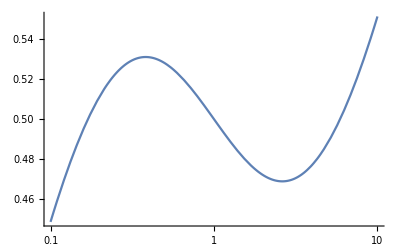

```mathematica
etaOfCPlt = LogLinearPlot[etaNC/.{DRhoOverT->.2,k->1},{c,0.1,10}, PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"etaNCOfCReceptorBinding.pdf", etaOfCPlt]
```